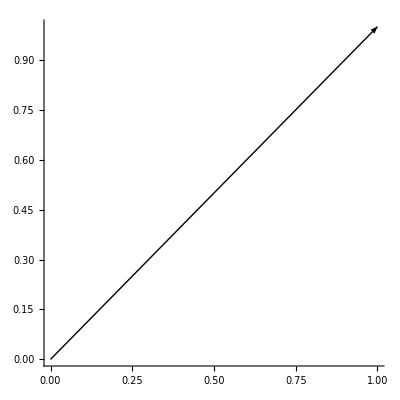

```mathematica
(*Rotation of a 2D vector*)
vector1 = {1,1};
Graphics[{Arrow[{{0,0},vector1}]},Axes->True](*Plot the vector in 2 Dimensional space*)
```

```mathematica
(*Now let's we want to rotate vector1 by some user inputted angle in the counterclockwise direction*)
(*We use matrices!*)
```

```mathematica
angle = Input["Enter angle in radians"];(*User inputted rotation angle*)
RotationMat = RotationMatrix[angle];(*We find the rotation matrix*)
RotationMat//MatrixForm
```

(1/2 | -(√3)/2
(√3)/2 | 1/2)

```mathematica
NewVector = RotationMat.vector1;
NewVector //MatrixForm
```

(1/2-(√3)/2
1/2+(√3)/2)

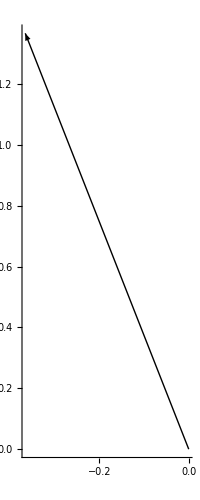

```mathematica
Graphics[{Arrow[{{0,0},NewVector}]},Axes->True](*Plot the new vector in 2 Dimensional space*)
```

```mathematica
(*Now we go to the 3-Dimensional case*)
```

```mathematica
vec1 = {1,2,3};
vec2 = {4,5,6};
vec3 = {5,6,7};
```

```mathematica
Graphics3D[Arrow[{{0,0,0},vec1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium]
```

-Graphics3D-

```mathematica
Graphics3D[Arrow[{{0,0,0},vec2}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium]
```

-Graphics3D-

```mathematica
Graphics3D[Arrow[{{0,0,0},vec3}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium]
```

-Graphics3D-

```mathematica
data={vec1,vec2,vec3};

Graphics3D[Arrow[{{0,0,0},#}]&/@data,Axes -> True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(*We can plot them together*)
```

```mathematica
(*Now say we want to rotate vec1 around the z axis by some user inputted angle*)
angleZ = Input["Enter angle in radians"];
Rotationz = RotationMatrix[angleZ, {0,0,1}];
Rotationz//MatrixForm
```

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
RotatedVec1 = Rotationz.vec1;
RotatedVec1//MatrixForm
```

(-1
-2
3)

```mathematica
Graphics3D[Arrow[{{0,0,0},RotatedVec1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large]
```

-Graphics3D-

```mathematica
(*In real game development, however, rotations are not that easy. You usually don't rotate about a fixed axes but need one vector to rotate in the direction of another vector*)
vec = Input["Enter the direction you want to rotate vec2 in"];
rotatemat2 = RotationMatrix[{vec2,vec}];
rotatemat2//MatrixForm;
```

```mathematica
(*Let's plot the rotated vec2*)
```

```mathematica
RotatedVec2 = rotatemat2.vec2;
RotatedVec2//MatrixForm
```

(1/385 (385-37 √154)+2/231 (77+31 √154)+1/462 (-770+59 √154)
2/231 (-154+13 √154)+1/231 (770+31 √154)+1/385 (-770+59 √154)
2/231 (77-5 √154)+5/462 (-154+13 √154)+1/77 (77+31 √154))

```mathematica
Graphics3D[Arrow[{{0,0,0},RotatedVec2}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large](*Plotting the new matrix*)
```

-Graphics3D-

```mathematica
rotate1 = RotationMatrix[{vec1,vec2}];(*gives the matrix that rotates vec1 in the direction of vec2*)
rotate1 //MatrixForm
```

(1/462 (77+80 √22) | 1/462 (-154+41 √22) | 1/462 (77+2 √22)
1/462 (-154+23 √22) | 2/231 (77+8 √22) | 1/462 (-154+41 √22)
1/462 (77-34 √22) | 1/462 (-154+23 √22) | 1/462 (77+80 √22))

```mathematica
Graphics3D[{Opacity[1],Cuboid[{-.5,-.5,-.5}]},Boxed->False](*Plotting just a plain cuboid*)
```

-Graphics3D-

```mathematica
Graphics3D[{{Opacity[1],Cuboid[{-.5,-.5,-.5}]},GeometricTransformation[Cuboid[{-.5,-.5,-.5}],rotate1]},Boxed->False](*Now plotting the same cuboid that is rotated by the vector rotate1*)
```

-Graphics3D-

```mathematica
rotate2 = RotationMatrix[{vec2,vec3}];(*gives the matrix that rotates vec2 in the direction of vec3*)
rotate2//MatrixForm
```

(1/462 (77+46 √70) | 1/462 (-154+19 √70) | 1/462 (77-8 √70)
(-770+89 √70)/2310 | (2 (385+23 √70))/1155 | 1/462 (-154+19 √70)
(385-52 √70)/2310 | (-770+89 √70)/2310 | 1/462 (77+46 √70))

```mathematica
Graphics3D[{{Opacity[1],Cuboid[{-.5,-.5,-.5}]},GeometricTransformation[Cuboid[{-.5,-.5,-.5}],rotate2]},Boxed->False](*Now plotting the same cuboid that is rotated by the vector rotate1*)
```

-Graphics3D-

```mathematica
(*Mathematica has this really cool feature whereby it gives you the matrix you require to transform vectors. Let's look at the following examples*)
```

```mathematica
r = RotationTransform[a]
```

```mathematica
TransformationFunction[({{Cos[a], -Sin[a], 0}, {Sin[a], Cos[a], 0}, {0, 0, 1}})]
(*This rotates the vector {1,2} by an angle a*)
r[{1,2}]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

{Cos[a]-2 Sin[a],2 Cos[a]+Sin[a]}

```mathematica
(*Or If I wanted to rotate a vector by some angle a around the z-axis. My transformation matrix is given by trans*)
```

```mathematica
trans = RotationTransform[a,{0,0,1}]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0 | 0
Sin[a] | Cos[a] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]

```mathematica
(*So we have finally got all our information to actually understand graphics*)
```

```mathematica
(*This cube rotates 360 degress about the z-axis*)
```

```mathematica
Manipulate[Graphics3D[Rotate[Cuboid[],a Degree,{0,0,1}]],{a,0,360}]
```

```mathematica
(*This rotates the cube about the Y-axis*)
Manipulate[Graphics3D[Rotate[Cuboid[],a Degree,{0,1,0}]],{a,0,360}]
```

```mathematica
(*Or just as simply rotated the cube around the X-axis*)
```

```mathematica
Manipulate[Graphics3D[Rotate[Cuboid[],a Degree,{1,0,0}]],{a,0,360}]
```

```mathematica
(*We could do the same with a cylinder rotated about the X axis*)
```

```mathematica
Manipulate[Graphics3D[Rotate[Cylinder[],a Degree,{1,0,0}]],{a,0,360}]
```

```mathematica
(*We could do the same with vectors which is perhaps a little more relevation to graphics design*)
```

```mathematica
Manipulate[Graphics[{Arrow[{{0,0},RotationMatrix[a].{1,1}}]},Axes->True],{a,0,2*Pi}]
```

```mathematica
(*We could even extrapolate this to the 3-Dimensional vector case*)
```

```mathematica
Manipulate[Graphics3D[Arrow[{{0,0,0},RotationMatrix[a,{0,0,1}].{1,2,3}}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium],{a,0,2*Pi}]
```